```mathematica
L = 0.076;
Fg = 0.2;
Remove[s]
s[α_, k_,Fd_, μ_, α0_] :=k(α0 - α)+ L (Fd+Fg) Sin[α]  - μ L( Fd + Fg) Cos[α]  - Fg*L/2*Sin[α]
```

```mathematica
alpha [ k_,Fd_, μ_, α0_]:= α /. NSolve[s[α,  k,Fd, μ, α0]== 0, α, Reals][[1]]
```

```mathematica
d[α_, α0_] := L(Sin[α0]- Sin[α])
```

```mathematica
maxFd[ k_, μ_, α0_] := Fd /.  NSolve[s[0,  k,Fd, μ, α0]== 0, Fd, Reals][[1]]
```

Experimental data:

```mathematica
(*exk = 0.14;
exFd = 1.2;
exmu = 0.7;
exa0 = 20*Pi/180;*)
```

```mathematica
Distance[ k_,Fd_, μ_, α0_] := d[alpha[k,Fd,μ, α0], α0]
```

Minimalny nacisk: alfa jest kątem blokera

```mathematica
minFd [α_, k_, μ_, α0_]:= Fd /. NSolve[s[α,  k,Fd, μ, α0]== 0, Fd, Reals][[1]]
```

```mathematica
forces = {0.8, 1.0, 1.1, 1.3, 1.4, 1.5, 1.6, 1.7, 1.8}
```

{0.8,1.,1.1,1.3,1.4,1.5,1.6,1.7,1.8}

```mathematica
ds = {3.2, 3.8, 4.7, 7.2, 10.2 , 12.6, 14.0, 16.0, 21.0}
```

{3.2,3.8,4.7,7.2,10.2,12.6,14.,16.,21.}

```mathematica
data = Transpose[{forces, ds}]
```

{{0.8,3.2},{1.,3.8},{1.1,4.7},{1.3,7.2},{1.4,10.2},{1.5,12.6},{1.6,14.},{1.7,16.},{1.8,21.}}

```mathematica
errors= 0.5+ds/20
```

{0.66,0.69,0.735,0.86,1.01,1.13,1.2,1.3,1.55}

```mathematica
dataWithError={#[[1]],Around[#[[2]],0.5+#[[2]]/20]}&/@data;
```

```mathematica
dataWithError
```

{{0.8,3.20.7},{1.,3.80.7},{1.1,4.70.7},{1.3,7.20.9},{1.4,10.21.0},{1.5,12.61.1},{1.6,14.01.2},{1.7,16.01.3},{1.8,21.01.6}}

```mathematica
exk = 2.2*L;
exFd = 1.2;
exmu = 0.40;
add = 1.7*Pi/180;
exa0 = 20*Pi/180;
```

```mathematica
L
exk
exmu
exa0
```

0.076

0.1672

0.4

π/9

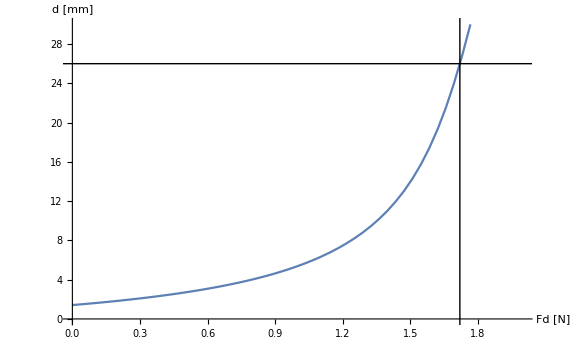

```mathematica
p0=Plot[1000*d[alpha[exk,Fd,exmu,exa0],exa0],{Fd,0,maxFd[exk,exmu,exa0]*1.05},Epilog->{InfiniteLine[{maxFd[exk,exmu,exa0],0},{0,1}], InfiniteLine[{0,L*Sin[exa0]*1000},{1,0}]},
PlotLabel->"",AxesLabel->{"Fd [N]","d [mm]"}, ImageSize->Large, PlotRange->{{0,2},{0,30}}]
```

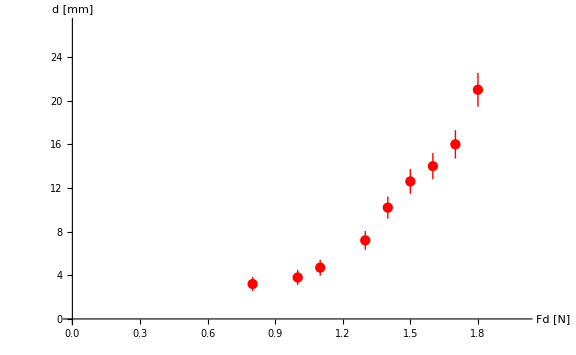

```mathematica
p1=ListPlot[dataWithError,PlotLabel->"",AxesLabel->{"Fd [N]","d [mm]"}, ImageSize->Large,PlotStyle->Red,PlotRange->{{0,2},{0,27}}]
```

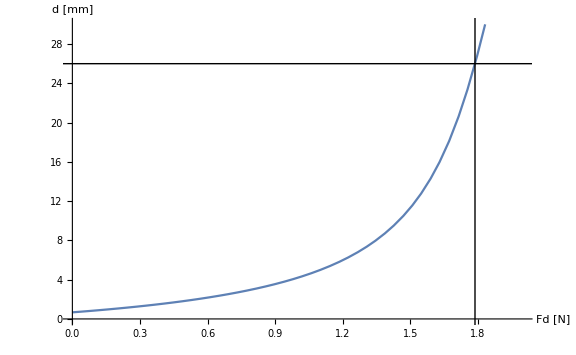

```mathematica
p2=Plot[1000*d[alpha[kfit,Fd,mufit,a0fit],exa0],{Fd,0,2},Epilog->{InfiniteLine[{maxFd[kfit,mufit,a0fit],0},{0,1}], InfiniteLine[{0,L*Sin[exa0]*1000},{1,0}]},
PlotLabel->"",AxesLabel->{"Fd [N]","d [mm]"}, ImageSize->Large, PlotRange->{{0,2},{0,30}}]
```

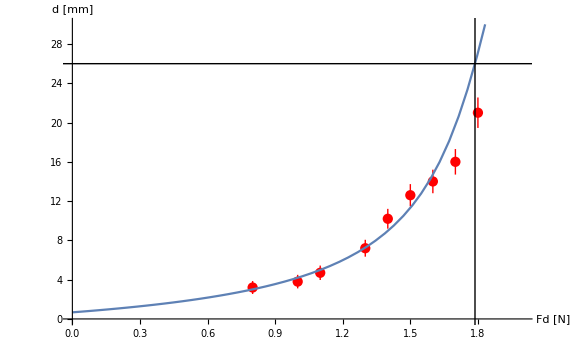

```mathematica
Show[p1,p2,Epilog->{InfiniteLine[{maxFd[kfit,mufit,a0fit],0},{0,1}], InfiniteLine[{0,L*Sin[exa0]*1000},{1,0}]},PlotRange->{{0,2},{0,30}}]
```

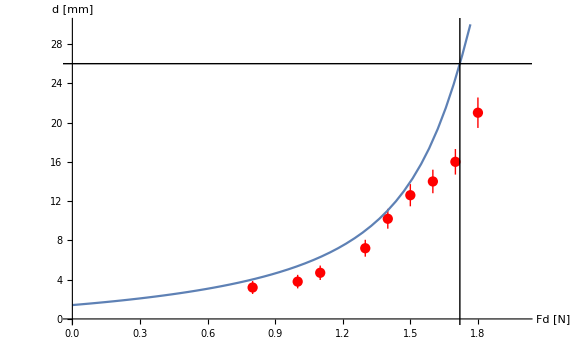

```mathematica
Show[p1,p0,Epilog->{InfiniteLine[{maxFd[exk,exmu,exa0],0},{0,1}], InfiniteLine[{0,L*Sin[exa0]*1000},{1,0}]},PlotRange->{{0,2},{0,30}}]
```

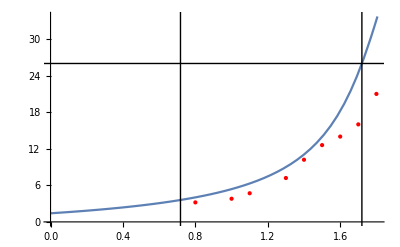

```mathematica
Plot[1000*d[alpha[exk,Fd,exmu,exa0],exa0],{Fd,0,maxFd[exk,exmu,exa0]*1.05},Epilog->{InfiniteLine[{minFd[exa0,exk,exmu,exa0+add],0},{0,1}],InfiniteLine[{maxFd[exk,exmu,exa0],0},{0,1}], InfiniteLine[{0,L*Sin[exa0]*1000},{1,0}],Red,PointSize[Medium],Point[data]}]
```

```mathematica
Plot[1000*d[alpha[exk,Fd,exmu,exa0],exa0],{Fd,0,maxFd[exk,exmu,exa0]*1.05},Epilog->{InfiniteLine[{minFd[exa0,exk,exmu,exa0+add],0},{0,1}],InfiniteLine[{maxFd[exk,exmu,exa0],0},{0,1}], InfiniteLine[{0,L*Sin[exa0]*1000},{1,0}],Red,PointSize[Medium],Point[data]}]
```

-Graphics-

```mathematica
((1000*d[alpha[exk,#,exmu,exa0],exa0]&/@forces)- ds)^2/errors^2
```

{1.55429,5.23641,4.73868,4.34853,0.715744,1.43322,12.1791,42.2999,61.3335}

```mathematica
Manipulate[Show[p1,Plot[1000*d[alpha[k,Fd,mu,a0],exa0],{Fd,0,2},ImageSize->Large, PlotRange->{{0,2},{0,30}}]],{{k,exk,"k"},exk*0.9,exk*1.1,Appearance->"Labeled"},{{mu,exmu,"mu"},exmu*0.9,exmu*1.1,Appearance->"Labeled"},{{a0,exa0,"a0"},exa0*0.9,exa0*1.1,Appearance->"Labeled"}]
```

```mathematica
data
```

{{0.8,3.2},{1.,3.8},{1.1,4.7},{1.3,7.2},{1.4,10.2},{1.5,12.6},{1.6,14.},{1.7,16.},{1.8,21.}}

```mathematica
model = 1000*d[alpha[k,Fd,mu,a0],exa0]
```

ReplaceAll::reps: {k (a0-α)-0.076 (0.2+Fd) mu Cos[α]-0.0076 Sin[α]+0.076 (0.2+Fd) Sin[α]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

76. (Sin[π/9]-Sin[α/.k (a0-α)-0.076 (0.2+Fd) mu Cos[α]-0.0076 Sin[α]+0.076 (0.2+Fd) Sin[α]==0])

```mathematica
kfit=0.17175
mufit = 0.4083
a0fit = 0.359
```

0.17175

0.4083

0.359

```mathematica
a0fit*180/Pi
```

20.5692